```mathematica
4+4
```

8

```mathematica
data = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData[All]}], {_, _Missing}];
Short[data]
```

{{Afghanistan,52.1 yr},{Albania,78.6 yr},{Algeria,77.2 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,60.6 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,76.9 yr},{Argentina,77.5 yr},{Armenia,75.1 yr},{Aruba,77.1 yr},{Australia,82.4 yr},«208»,{United States Virgin Islands,79.5 yr},{Uruguay,77.6 yr},{Uzbekistan,74.3 yr},{Vanuatu,74. yr},{Venezuela,76.2 yr},{Vietnam,73.9 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,63.8 yr},{Yemen,66.2 yr},{Zambia,53. yr},{Zimbabwe,61.1 yr}}

```mathematica
Short[SortBy[data, Last]]
```

{{Afghanistan,52.1 yr},{Lesotho,53. yr},{Zambia,53. yr},{Somalia,53.2 yr},{Central African Republic,53.3 yr},{Mozambique,54.1 yr},{Niger,56.3 yr},{Uganda,56.3 yr},{South Sudan,56.811 yr},{Chad,57.5 yr},{Eswatini,57.754 yr},{Democratic Republic of the Congo,58.1 yr},«208»,{Guernsey,82.7 yr},{Israel,82.7 yr},{Malta,82.7 yr},{Switzerland,82.7 yr},{Andorra,82.9 yr},{Hong Kong,83.1 yr},{Iceland,83.1 yr},{San Marino,83.4 yr},{Macau,84.6 yr},{Japan,85.5 yr},{Singapore,85.5 yr},{Monaco,89.4 yr}}

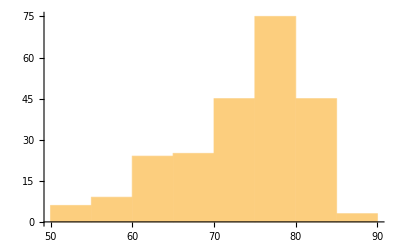

```mathematica
Histogram[data⟦All,2⟧]
```

```mathematica
dataAfrica = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["Africa"]}],{_,_Missing}];
Mean[dataAfrica⟦All,2⟧]
```

64.3565 yr

```mathematica
dataAsia = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["Asia"]}],{_,_Missing}];
Mean[dataAsia⟦All,2⟧]
```

74.2019 yr

```mathematica
dataEurope = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["Europe"]}], {_,_Missing}];
Mean[dataEurope⟦All,2⟧]
```

79.4707 yr

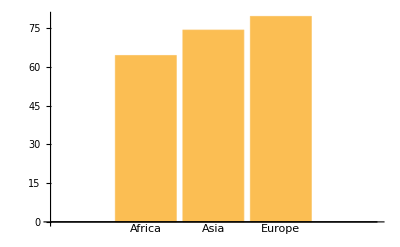

```mathematica
BarChart[{Mean[dataAfrica⟦All,2⟧],Mean[dataAsia⟦All,2⟧],Mean[dataEurope⟦All,2⟧]},
ChartLabels->{"Africa","Asia","Europe"}]
```

```mathematica
dataSouthAmerica=DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["SouthAmerica"]}],{_,_Missing}];
Take[dataSouthAmerica, 3]
```

{{Argentina,77.5 yr},{Bolivia,69.8 yr},{Brazil,74.3 yr}}

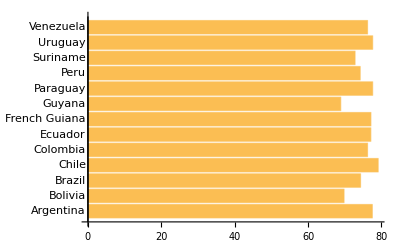

```mathematica
BarChart[dataSouthAmerica⟦All,2⟧,ChartLabels->dataSouthAmerica⟦All,1⟧,
BarOrigin->Left]
```

```mathematica
data=DeleteCases[
Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"GDP"]},CountryData[i,"Name"]],{i,CountryData[]}],
{_,_Missing}];
ListLogLogPlot[data, AxesLabel->{"Life Expectancy","GDP"}]
```

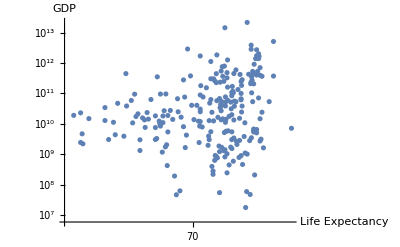

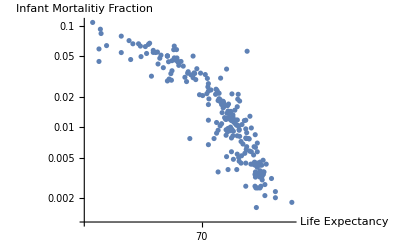

```mathematica
data =
Table[
Tooltip[{CountryData[i, "LifeExpectancy"],CountryData[i,"InfantMortalityFraction"]},
CountryData[i,"Name"]],{i,CountryData[]}];
ListLogLogPlot[data,AxesLabel->{"Life Expectancy","Infant Mortalitiy Fraction"}]
```

```mathematica
Manipulate[plotFn[Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,prop]},CountryData[i,"Name"]],{i,CountryData["EU"]}],AxesLabel->{"Life Expectancy",prop}],{prop,{"InfantMortalityFraction","GDP","LiteracyFraction"}},SaveDefinitions->True]
```

```mathematica
Clear[data,dataAfrica,dataAsia,dataEurope,dataSouthAmerica]
```